```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Can be used for Dirichlet and traction BCs *)
(* Desired solution *)
u[x_,y_,t_]:=x Cos[t];
v[x_,y_,t_]:= y Cos[t];
p[x_,y_,t_]:=Sin[x] Sin[y] Sin[t];
d[x_,y_]:=0.1-Sqrt[(x)^2+(y)^2];
ρ[x_,y_,t_]:=1.0;(*ρ0+ρ1/2(1+Tanh[d[x,y]/δ])+x Cos[Sin[t]] + y Sin[Sin[t]] + 2;*)
μ[x_,y_,t]:= 1.0;
```

```mathematica
tau11[x_,y_,t_]=  D[u[x,y,t],x];
tau12[x_,y_,t_] = 1/2(D[u[x,y,t],y]+ D[v[x,y,t],x]);
tau22[x_,y_,t_]=  D[v[x,y,t],y];
```

```mathematica
(* Divergence free? *)
-(D[u[x,y,t],x]+D[v[x,y,t],y])
```

-2 Cos[t]

```mathematica
mass = Simplify[D[ρ[x,y,t], t] + D[ρ[x,y,t]u[ x,y,t],x] + D[ρ[ x,y,t]v[x,y,t],y]]
```

2. Cos[t]

```mathematica
(* Required forcing function *)
fx[x_,y_,t_]= (D[ρ[x,y,t]u[x,y,t],t] + D[ρ[x,y,t]u[x,y,t]u[x,y,t],x] +  D[ρ[x,y,t]v[x,y,t]u[x,y,t],y]) + D[p[x,y,t],x] - 2(D[μ[x,y,t] tau11[x,y,t],x]+D[μ[x,y,t] tau12[x,y,t],y])
fy[x_,y_,t_]= (D[ρ[x,y,t]v[x,y,t],t] + D[ρ[x,y,t]u[x,y,t]v[x,y,t],x] +  D[ρ[x,y,t]v[x,y,t]v[x,y,t],y]) + D[p[x,y,t],y] - 2(D[μ[x,y,t] tau12[x,y,t],x]+D[μ[x,y,t]tau22[x,y,t],y])

fx[x_,y_,t_]= FullSimplify[ D[ρ[x,y,t]u[x,y,t],t]+D[p[x,y,t],x] - 2(D[μ[x,y,t] tau11[x,y,t],x]+D[μ[x,y,t] tau12[x,y,t],y])]

fy[x_,y_,t_]= FullSimplify[ D[ρ[x,y,t]v[x,y,t],t]+D[p[x,y,t],y] - 2(D[μ[x,y,t] tau12[x,y,t],x]+D[μ[x,y,t]tau22[x,y,t],y])]
```

3. x Cos[t]^2-4 π μ1 Cos[t] Cos[2 π x] Cos[2 π y]-1. x Sin[t]+Cos[x] Sin[t] Sin[y]

3. y Cos[t]^2-1. y Sin[t]+Cos[y] Sin[t] Sin[x]+4 π μ1 Cos[t] Sin[2 π x] Sin[2 π y]

-4 π μ1 Cos[t] Cos[2 π x] Cos[2 π y]+Sin[t] (-1. x+Cos[x] Sin[y])

Sin[t] (-1. y+Cos[y] Sin[x])+4 π μ1 Cos[t] Sin[2 π x] Sin[2 π y]

```mathematica
(*Periodic forces?*)
fx[0,y,t]-fx[1,y,t]
fy[0,y,t]-fy[1,y,t]
fx[x,0,t]-fx[x,0,t]
fy[x,1,t]-fy[x,1,t]
```

Sin[t] (0.+Sin[y])-Sin[t] (-1.+Cos[1] Sin[y])

-1. y Sin[t]-(-1. y+Cos[y] Sin[1]) Sin[t]

0.

0

```mathematica
Manipulate[ContourPlot[v[x,y,t],{x,0,1},{y,0,1},Contours->10],{t,0,0.001}]
```

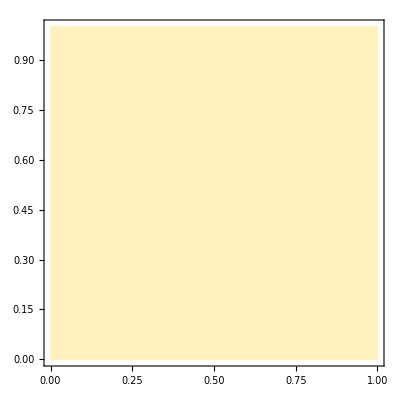

1.

```mathematica
ρ0 = 1.0;
ρ1 = -1.0+1000;
δ = 0.01;
ContourPlot[ρ[x,y,0],{x,0,1},{y,0,1},Contours->20]
ρ[0.5,0.5,0]/ρ[1,1,0]
```

```mathematica
D[p[x,y,t],x]//FullSimplify
```

Cos[x] Sin[t] Sin[y]

```mathematica
D[p[x,y,t],y]//FullSimplify
```

Cos[y] Sin[t] Sin[x]

```mathematica
CellPrint[[HoldForm[fx[x,y,t]],"Output",AutoMultiplicationSymbol->True]]
```

CellPrint⟦fx[x,y,t],Output,AutoMultiplicationSymbol→True⟧

```mathematica
fy[x,y,t]//InputForm
```

Sin[t]*(-1.*y + Cos[y]*Sin[x]) + 4*Pi*μ1*Cos[t]*Sin[2*Pi*x]*Sin[2*Pi*y]

```mathematica
ρ0 = 1.0;
ρ1 = 1.0+10;
μ0 = 0.001;
μ1 = -μ0+1;
δ = 0.01;
Manipulate[ContourPlot[fy[x,y,t],{x,0,1},{y,0,1},Contours->10,PlotLegends->Automatic],{t,0,0.1}]
```

```mathematica
(*Tangential traction at top and bottom face*)
μ[x,y,t](D[u[x,y,t],y]+ D[v[x,y,t],x])
```

0

```mathematica
(*Normal traction at top and bottom face*)
-p[x,y,t]+2μ[x,y,t]D[v[x,y,t],y]//InputForm
```

2*Cos[t]*(1. + 0.999*Cos[2*Pi*y]*Sin[2*Pi*x]) - Sin[t]*Sin[x]*Sin[y]

```mathematica
trac[x_,y_,t_]=-p[x,y,t]+2μ[x,y,t]D[v[x,y,t],y]
```

2 Cos[t] (1.+0.999 Cos[2 π y] Sin[2 π x])-Sin[t] Sin[x] Sin[y]

```mathematica
trac[0,1,t]-trac[1,1,t]
```

0.+Sin[1]^2 Sin[t]